## Setup

```mathematica
R=10;
n=11;
h=R/(n-1)
```

1

```mathematica
symm[i_]=If[i>=1,i,2-i];
```

```mathematica
(grad2=1/h Table[
(If[j==symm[i-1],-1,0]+
If[j==symm[i+1],+1,0])/2,
{i,n},{j,n}])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0)

```mathematica
(grad4=1/h Table[
(If[j==symm[i-2],+1,0]+
If[j==symm[i-1],-8,0]+
If[j==symm[i+1],+8,0]+
If[j==symm[i+2],-1,0])/12,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(grad6=1/h Table[
(If[j==symm[i-3],-1,0]+
If[j==symm[i-2],+9,0]+
If[j==symm[i-1],-180/4,0]+
If[j==symm[i+1],180/4,0]+
If[j==symm[i+2],-9,0]+
If[j==symm[i+3],+1,0])/60,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(grad8=1/h Table[
(     If[j==symm[i-4],+1,0]+
If[j==symm[i-3],-(280*4)/105,0]+
If[j==symm[i-2],+280/5,0]+
If[j==symm[i-1],-280*4/5,0]+
If[j==symm[i+1],+280*4/5,0]+
If[j==symm[i+2],-280/5,0]+
If[j==symm[i+3],+(280*4)/105,0]+
If[j==symm[i+4],-1,0])/280,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(W=h DiagonalMatrix[
Table[If[i==1,1/2,1],
{i,n}]
])//MatrixForm;
```

```mathematica
(B=DiagonalMatrix[Table[0,{i,n}]])//MatrixForm;
B[[n,n]]=0;
B//MatrixForm;
```

```mathematica
(div2=Inverse[W].Transpose[B-W.grad2])//MatrixForm;
(div4=Inverse[W].Transpose[B-W.grad4])//MatrixForm;
(div6=Inverse[W].Transpose[B-W.grad6])//MatrixForm;
(div8=Inverse[W].Transpose[B-W.grad8])//MatrixForm;
```

```mathematica
(QS=DiagonalMatrix[Table[q[i],{i,n}]])//MatrixForm;
```

```mathematica
(c=Table[1,{i,n}])//MatrixForm;
```

```mathematica
(r=h Table[i-1,{i,n}])//MatrixForm;
div2.r-1
```

{0,0,0,0,0,0,0,0,0,0,-11/2}

```mathematica
grad2.r^2-2r
```

{0,0,0,0,0,0,0,0,0,0,-121/2}

```mathematica
div4.r^3-3 r^2
```

{0,0,0,0,0,0,0,0,0,1331/12,-2230/3}

```mathematica
grad4.r^4-4 r^3
```

{0,0,0,0,0,0,0,0,0,14641/12,-24098/3}

```mathematica
div6.r
```

{1,1,1,1,1,1,1,1,49/60,49/20,-17/3}

```mathematica
l=0;
kk=Join[{0},Table[BesselJZero[1/2 (1+2 l),i]/R,{i,1,n-1}]];
λ=-N[kk^2];
plot0=Plot[λ,{x,.2,1},PlotStyle->Red,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

## 2nd Order

(q[1.]→0.497512
q[2.]→1.49254
q[3.]→4.47761
q[4.]→9.45274
q[5.]→16.4179
q[6.]→25.3731
q[7.]→36.3184
q[8.]→49.2537
q[9.]→64.1791
q[10.]→81.0945
q[11.]→100.)

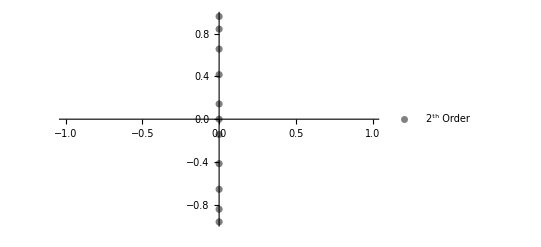

```mathematica
(cond2=div2.QS.r-3QS.c)//MatrixForm;
cond22=Join[cond2[[1;;-2]],{q[n]-r[[n]]^2}];
(sol2=Solve[cond22==0,Table[q[i],{i,n}]][[1]])//MatrixForm//N
QQS2=QS/.sol2;
DDIV2=Inverse[QQS2].div2.QQS2;
DDIV2.r//FullSimplify;
(vals2=Eigenvalues[DDIV2])//N//MatrixForm;
cplot2=ComplexListPlot[vals2,AspectRatio->1/GoldenRatio,PlotStyle->Gray,PlotLegends->{"2^th Order"},PlotRange->All]
```

## 4th Order

```mathematica
order=3;
```

```mathematica
(QV4= QS
+Table[Which[i≤order&&j≤order,
Which[
j>i,q[i,j],
j<i,q[j,i],
True,0],
True,0],{i,n},{j,n}]
)//MatrixForm
```

(q[1] | q[1,2] | q[1,3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,2] | q[2] | q[2,3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,3] | q[2,3] | q[3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | q[4] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | q[5] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | q[6] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | q[7] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | q[8] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[9] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[10] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[11])

```mathematica
QS4 = QV4;(*Use the same norm for scalars as for vectors (non diagonal)*)
```

```mathematica
(cond4a=Inverse[QS4].div4.QV4.r-3c)//MatrixForm;
(cond4b=Inverse[QS4].div4.QV4.r^3-5 r^2)//MatrixForm;
```

```mathematica
(*(cond4=Join[
cond4a[[;;-3]],
cond4b[[;;3]],
{q[1]-100/201,q[2]-100/67(*,q[3]-300/67*)(*,q[4]-1900/201,q[5]-1100/67,q[5]-1100/67,q[6]-1700/67,q[7]-7300/201,
q[8]-3300/67,q[9]-4300/67,*)(*q[n-2]-r[[n-2]]^2,q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2*)}])//MatrixForm;*)
```

```mathematica
(cond4=Join[
cond4a[[;;-3]],
cond4b[[;;3]],
{q[n-1]-(r[[n-1]]^2),
q[n]-(r[[n]]^2)}])//MatrixForm;
(vars4 = DeleteDuplicates[SparseArray[QV4]["NonzeroValues"]])//MatrixForm;
(*RealQ[x_]:=!(Element[x,Reals]===True)
vars =Select[vars,RealQ];*)
Length[vars4]
Length[cond4]
```

14

14

```mathematica
(solq4=Solve[cond4==0,vars4][[1]])//MatrixForm//N
```

(q[1.]→5.59796
q[1.,2.]→-4.77546
q[1.,3.]→0.508325
q[2.]→7.21504
q[2.,3.]→-1.64102
q[3.]→4.57512
q[4.]→9.13093
q[5.]→15.9378
q[6.]→25.0311
q[7.]→35.9748
q[8.]→49.0081
q[9.]→63.9832
q[10.]→81.
q[11.]→100.)

```mathematica
(QQS4 = QV4/.solq4)//MatrixForm//N;
QQV4=QV4/.solq4;
```

```mathematica
PositiveDefiniteMatrixQ[QQS4/.h->1]
```

True

```mathematica
(DDIV4 = Inverse[QQS4].div4.QQV4)//N//MatrixForm
```

(-2.33422 | 3.41727 | -0.250723 | 0.131345 | -0.0774655 | 0. | 0. | 0. | 0. | 0. | 0.
-1.33445 | 1.8525 | 0.366355 | 0.305713 | -0.125587 | 0. | 0. | 0. | 0. | 0. | 0.
0.476562 | -0.766564 | 0.398385 | 1.42558 | -0.326738 | 0. | 0. | 0. | 0. | 0. | 0.
-0.080697 | 0.185662 | -0.349015 | 0. | 1.16365 | -0.228446 | 0. | 0. | 0. | 0. | 0.
0.00265786 | -0.00858034 | 0.0239217 | -0.38194 | 0. | 1.04703 | -0.1881 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0303987 | -0.42448 | 0. | 0.958138 | -0.163157 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0369189 | -0.463863 | 0. | 0.908192 | -0.148213 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0425628 | -0.489373 | 0. | 0.870377 | -0.137732 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0468545 | -0.510634 | 0. | 0.843971 | -0.130242
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0504198 | -0.526611 | 0. | 0.823045
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0533194 | -0.54 | 0.)

```mathematica
DDIV4.r//FullSimplify//MatrixForm//N
```

(3.
3.
3.
3.
3.
3.
3.
3.
3.
4.3705
-4.43345)

```mathematica
(DDIV4.r^3-5 r^2)[[;;5]]//FullSimplify//MatrixForm//N
```

(0.
0.
0.
-1.68864
0.119738)

```mathematica
(vals4=Eigenvalues[N[DDIV4]])//MatrixForm
```

(-0.0012804+1.30938 ⅈ
-0.0012804-1.30938 ⅈ
-0.00463976+1.13047 ⅈ
-0.00463976-1.13047 ⅈ
-0.0088423+0.86118 ⅈ
-0.0088423-0.86118 ⅈ
-0.0124524+0.534631 ⅈ
-0.0124524-0.534631 ⅈ
-0.0144518+0.180655 ⅈ
-0.0144518-0.180655 ⅈ
-4.71932×10^-15+0. ⅈ)

```mathematica
SpectralRadius=Max[Norm[vals4]]
```

2.84711

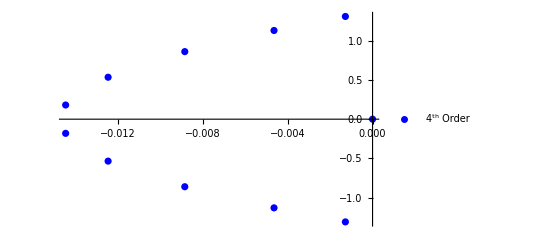

```mathematica
cplot4=ComplexListPlot[vals4,AspectRatio->1/GoldenRatio, PlotStyle->Blue, PlotLegends->{"4^th Order"},PlotRange->All]
```

```mathematica
(lvals4=Sort[Eigenvalues[N[DDIV4.grad4]]])//MatrixForm
```

(-2.87772
-1.76847
-1.70501
-1.30225
-1.18372
-0.772695
-0.591491
-0.323591
-0.210974
-0.105241
-3.37886×10^-16)

```mathematica
(λ[[-1]]/lvals4[[1]])
```

3.42966

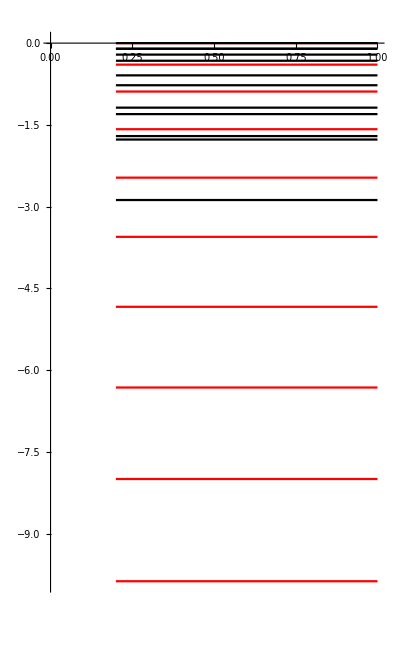

```mathematica
plot4=Plot[lvals4,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},All},PlotLabel->"6th Order"];
Show[plot0, plot4]
```

## 6th Order

```mathematica
order=5;
(QS6= QV
+Table[Which[i≤order&&j≤order,
Which[
j>i+1,q[i,j],
j<i-1,q[j,i],
True,0],
True,0],{i,n},{j,n}]
+Table[If[i≤n-2&& j≤n-2,Which[j==i+1,q[i,j],j==i-1,q[j,i],True,0],0],{i,n},{j,n}]
)//MatrixForm
```

(QV | QV+q[1,2] | QV+q[1,3] | QV+q[1,4] | QV+q[1,5] | QV | QV | QV | QV | QV | QV
QV+q[1,2] | QV | QV+q[2,3] | QV+q[2,4] | QV+q[2,5] | QV | QV | QV | QV | QV | QV
QV+q[1,3] | QV+q[2,3] | QV | QV+q[3,4] | QV+q[3,5] | QV | QV | QV | QV | QV | QV
QV+q[1,4] | QV+q[2,4] | QV+q[3,4] | QV | QV+q[4,5] | QV | QV | QV | QV | QV | QV
QV+q[1,5] | QV+q[2,5] | QV+q[3,5] | QV+q[4,5] | QV | QV+q[5,6] | QV | QV | QV | QV | QV
QV | QV | QV | QV | QV+q[5,6] | QV | QV+q[6,7] | QV | QV | QV | QV
QV | QV | QV | QV | QV | QV+q[6,7] | QV | QV+q[7,8] | QV | QV | QV
QV | QV | QV | QV | QV | QV | QV+q[7,8] | QV | QV+q[8,9] | QV | QV
QV | QV | QV | QV | QV | QV | QV | QV+q[8,9] | QV | QV | QV
QV | QV | QV | QV | QV | QV | QV | QV | QV | QV | QV
QV | QV | QV | QV | QV | QV | QV | QV | QV | QV | QV)

```mathematica
QS6=({{q[1], q[1,2], q[1,3], q[1,4], q[1,5], 0, 0, 0, 0, 0, 0}, {q[1,2], q[2], q[2,3], q[2,4], q[2,5], 0, 0, 0, 0, 0, 0}, {q[1,3], q[2,3], q[3], q[3,4], q[3,5], 0, 0, 0, 0, 0, 0}, {q[1,4], q[2,4], q[3,4], q[4], q[4,5], q[4,6], 0, 0, 0, 0, 0}, {q[1,5], q[2,5], q[3,5], q[4,5], q[5], q[5,6], q[5,7], 0, 0, 0, 0}, {0, 0, 0, q[4,6], q[5,6], q[6], q[6,7], q[6,8], 0, 0, 0}, {0, 0, 0, 0, q[5,7], q[6,7], q[7], q[7,8], 0, 0, 0}, {0, 0, 0, 0, 0, q[6,8], q[7,8], q[8], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, q[9], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, q[10], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[11]}});
```

```mathematica
(cond6a=div6.QV.r-3QS6.c)//MatrixForm;
(cond6b=div6.QV.r^3-5QS6.r^2)//MatrixForm;
(cond6c=div6.QV.r^5-7QS6.r^4)//MatrixForm;
(cond6d=div6.QV.r^7-9QS6.r^6)//MatrixForm;
```

```mathematica
(*(cond6=Join[
cond6a[[;;-4]],
cond6b[[;;-4]],
cond6c[[;;5]],
{q[n-2]-r[[n-2]]^2,
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}])//MatrixForm;*)
(* this produces the same spectrum as the 4th order!
QS6=({{q[1], q[1,2], q[1,3], q[1,4], 0, 0, 0, 0, 0, 0, 0}, {q[1,2], q[2], q[2,3], q[2,4], q[2,5], 0, 0, 0, 0, 0, 0}, {q[1,3], q[2,3], q[3], q[3,4], q[3,5], q[3,6], 0, 0, 0, 0, 0}, {q[1,4], q[2,4], q[3,4], q[4], q[4,5], q[4,6], 0, 0, 0, 0, 0}, {0, q[2,5], q[3,5], q[4,5], q[5], q[5,6], 0, 0, 0, 0, 0}, {0, 0, q[3,6], q[4,6], q[5,6], q[6], q[6,7], 0, 0, 0, 0}, {0, 0, 0, 0, 0, q[6,7], q[7], q[7,8], 0, 0, 0}, {0, 0, 0, 0, 0, 0, q[7,8], q[8], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, q[9], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, q[10], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[11]}});
(cond6=Join[
cond6a[[;;-4]],
cond6b[[;;-4]],
cond6c[[;;6]],
{q[n-2]-r[[n-2]]^2,
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}])//MatrixForm;*)
```

```mathematica
(cond6=Join[
cond6a[[;;-4]],
cond6b[[;;-4]],
cond6c[[;;7]],
{q[1]-2/3,
q[n-2]-r[[n-2]]^2,
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}])//MatrixForm;
(vars6 = DeleteDuplicates[SparseArray[QS6]["NonzeroValues"]])//MatrixForm;
(*RealQ[x_]:=!(Element[x,Reals]===True)
vars =Select[vars,RealQ];*)
Length[vars6]
Length[cond6]
```

27

27

```mathematica
(solq6=Solve[cond6==0,vars6][[1]])//MatrixForm//N
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
(QQS6 = QS6/.solq6)//MatrixForm//N
QQV6=QV/.solq6;
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
PositiveDefiniteMatrixQ[QQS6]
```

False

```mathematica
(DDIV6 = Inverse[QQS6].div6.QQV6)//MatrixForm;
```

```mathematica
DDIV6.r//FullSimplify//MatrixForm//N
```

Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}

```mathematica
(DDIV6.r^3-5 r^2)//FullSimplify//MatrixForm//N
```

(Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-5.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-20.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-45.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-80.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-125.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-180.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-245.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-320.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-405.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-500.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.})

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-5.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-20.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-45.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-80.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-125.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-180.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-245.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-320.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-405.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}
-500.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.})

```mathematica
(DDIV6.r^5-7 r^4)//FullSimplify//MatrixForm//N
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}
-7.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}
-112.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}
-567.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}
-1792.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}
-4375.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}
-9072.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}
-16807.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}
-28672.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}
-45927.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}
-70000.+Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.})

```mathematica
(vals6=Eigenvalues[N[DDIV6]])//MatrixForm
```

Eigenvalues[Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧)]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Eigenvalues[Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧)]

```mathematica
cplot6=ComplexListPlot[vals6,AspectRatio->1/GoldenRatio,PlotRange->All, PlotLabel->"Eigenvalues of Div6-nondiag",PlotStyle->Green,PlotLegends->{"6^th Order"}]
```

ComplexListPlot::ldata: Eigenvalues[Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},«9»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,«7»,0.,0.},«9»,{«1»}}.(QV/.{}⟦1⟧)] is not a valid dataset or list of datasets.

General::stop: Further output of ComplexListPlot::ldata will be suppressed during this calculation.

ComplexListPlot[vals6,AspectRatio→1/GoldenRatio,PlotRange→All,PlotLabel→Eigenvalues of Div6-nondiag,PlotStyle→Green,PlotLegends→{6^th Order}]

```mathematica
(lvals6=Sort[Eigenvalues[N[DDIV6.grad6]]])//MatrixForm
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Eigenvalues[Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.75,0.15,0.733333,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.15,-0.766667,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}]

```mathematica
(λ[[-1]]/lvals6[[1]])
```

-(9.8696/Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.75,0.15,0.733333,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.15,-0.766667,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}})

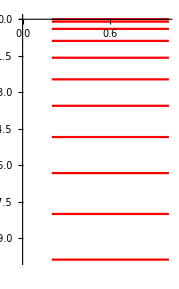

```mathematica
plot6=Plot[lvals6(**(λ[[-1]]/lvals6[[1]])*),{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},All},PlotLabel->"6th Order"];
Show[plot0, plot6]
```

## 8th Order

```mathematica
order=6;
(QS8= QV
+Table[Which[i≤order&&j≤order,
Which[
j>i+2,q[i,j],
j<i-2,q[j,i],
True,0],
True,0],{i,n},{j,n}]
+Table[If[i≤n-4&& j≤n-4,Which[j==i+1,q[i,j],j==i-1,q[j,i],True,0],0],{i,n},{j,n}]
+Table[If[i≤n-4&& j≤n-4,Which[j==i+2,q[i,j],j==i-2,q[j,i],True,0],0],{i,n},{j,n}]
)//MatrixForm
```

(QV | QV+q[1,2] | QV+q[1,3] | QV+q[1,4] | QV+q[1,5] | QV+q[1,6] | QV | QV | QV | QV | QV
QV+q[1,2] | QV | QV+q[2,3] | QV+q[2,4] | QV+q[2,5] | QV+q[2,6] | QV | QV | QV | QV | QV
QV+q[1,3] | QV+q[2,3] | QV | QV+q[3,4] | QV+q[3,5] | QV+q[3,6] | QV | QV | QV | QV | QV
QV+q[1,4] | QV+q[2,4] | QV+q[3,4] | QV | QV+q[4,5] | QV+q[4,6] | QV | QV | QV | QV | QV
QV+q[1,5] | QV+q[2,5] | QV+q[3,5] | QV+q[4,5] | QV | QV+q[5,6] | QV+q[5,7] | QV | QV | QV | QV
QV+q[1,6] | QV+q[2,6] | QV+q[3,6] | QV+q[4,6] | QV+q[5,6] | QV | QV+q[6,7] | QV | QV | QV | QV
QV | QV | QV | QV | QV+q[5,7] | QV+q[6,7] | QV | QV | QV | QV | QV
QV | QV | QV | QV | QV | QV | QV | QV | QV | QV | QV
QV | QV | QV | QV | QV | QV | QV | QV | QV | QV | QV
QV | QV | QV | QV | QV | QV | QV | QV | QV | QV | QV
QV | QV | QV | QV | QV | QV | QV | QV | QV | QV | QV)

```mathematica
(*QS8=({{q[1], q[1,2], q[1,3], q[1,4], q[1,5], q[1,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,2], q[2], q[2,3], q[2,4], q[2,5], q[2,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,3], q[2,3], q[3], q[3,4], q[3,5], q[3,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,4], q[2,4], q[3,4], q[4], q[4,5], q[4,6], q[4,7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,5], q[2,5], q[3,5], q[4,5], q[5], q[5,6], q[5,7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,6], q[2,6], q[3,6], q[4,6], q[5,6], q[6], q[6,7], q[6,8], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, q[4,7], q[5,7], q[6,7], q[7], q[7,8], q[7,9], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, q[6,8], q[7,8], q[8], q[8,9], q[8,10], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, q[7,9], q[8,9], q[9], q[9,10], q[9,11], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, q[8,10], q[9,10], q[10], q[10,11], q[10,12], 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, q[9,11], q[10,11], q[11], q[11,12], q[11,13], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, q[10,12], q[11,12], q[12], q[12,13], q[12,14], 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[11,13], q[12,13], q[13], q[13,14], q[13,15], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[12,14], q[13,14], q[14], q[14,15], q[14,16], 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[13,15], q[14,15], q[15], q[15,16], q[15,17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[14,16], q[15,16], q[16], q[16,17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[15,17], q[16,17], q[17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[18], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[19], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[20], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[21]}})*)
```

```mathematica
(cond8a=div8.QV.r^1-3QS8.c)//MatrixForm;
(cond8b=div8.QV.r^3-5QS8.r^2)//MatrixForm;
(cond8c=div8.QV.r^5-7QS8.r^4)//MatrixForm;
(cond8d=div8.QV.r^7-9QS8.r^6)//MatrixForm;
```

```mathematica
G[q1_]:=
Module[{u},
cond8G=Join[
cond8a[[;;-5]],
cond8b[[;;-5]],
cond8c[[;;-5]],
cond8d[[;;4]],
{q[1]-q1,
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}
];vars8G = DeleteDuplicates[SparseArray[QS8]["NonzeroValues"]];solq8G=Solve[cond8G==0,vars8G][[1]];QQS8G = QS8/.solq8G;QQV8G=QV/.solq8G;DDIV8G= N[Inverse[QQS8G].div8.QQV8G];((DDIV8G.r^7-9.0 r^6)[[1]])^2]
```

```mathematica
(*q1sol=NMinimize[{G[k],k≥0.0,k≤1},k]*)
```

```mathematica
(*FindMinimum[{G[k],k≥0.0,k≤1},{k,100419445/108274511 h^2}]*)
```

```mathematica
(*q10=q1sol[[2]][[1]]// Values;*)
```

```mathematica
(*q1Rational = Rationalize[N[q10],10^-16]*)
```

```mathematica
(cond8=Join[
cond8a[[;;-5]],
cond8b[[;;-5]],
cond8c[[;;-5]],
cond8d[[;;4]],
{(*q[1]-2045027588481283/2251799813685248,*)
(*q[1]-q1Rational,*)
q[1]-h^2,
(*q[n-2]-r[[n-2]]^2,*)
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}
])//MatrixForm;
(vars8 = DeleteDuplicates[SparseArray[QS8]["NonzeroValues"]])//MatrixForm;
Length[vars8]
Length[cond8]
```

18

28

```mathematica
(solq8=Solve[cond8==0,vars8][[1]])//MatrixForm//N
```

Solve::ivar: QV+q[1,2] is not a valid variable.

{{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[1.,2.]+q[1.,3.]+q[1.,4.]+q[1.,5.]+q[1.,6.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[1.,2.]+q[2.,3.]+q[2.,4.]+q[2.,5.]+q[2.,6.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[1.,3.]+q[2.,3.]+q[3.,4.]+q[3.,5.]+q[3.,6.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[1.,4.]+q[2.,4.]+q[3.,4.]+q[4.,5.]+q[4.,6.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[1.,5.]+q[2.,5.]+q[3.,5.]+q[4.,5.]+q[5.,6.]+q[5.,7.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[1.,6.]+q[2.,6.]+q[3.,6.]+q[4.,6.]+q[5.,6.]+q[6.,7.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[5.,7.]+q[6.,7.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (331. QV+q[1.,2.]+4. (QV+q[1.,3.])+9. (QV+q[1.,4.])+16. (QV+q[1.,5.])+25. (QV+q[1.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (331. QV+4. (QV+q[2.,3.])+9. (QV+q[2.,4.])+16. (QV+q[2.,5.])+25. (QV+q[2.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (335. QV+q[2.,3.]+9. (QV+q[3.,4.])+16. (QV+q[3.,5.])+25. (QV+q[3.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (340. QV+q[2.,4.]+4. (QV+q[3.,4.])+16. (QV+q[4.,5.])+25. (QV+q[4.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (311. QV+q[2.,5.]+4. (QV+q[3.,5.])+9. (QV+q[4.,5.])+25. (QV+q[5.,6.])+36. (QV+q[5.,7.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (320. QV+q[2.,6.]+4. (QV+q[3.,6.])+9. (QV+q[4.,6.])+16. (QV+q[5.,6.])+36. (QV+q[6.,7.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (344. QV+16. (QV+q[5.,7.])+25. (QV+q[6.,7.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (24355. QV+q[1.,2.]+16. (QV+q[1.,3.])+81. (QV+q[1.,4.])+256. (QV+q[1.,5.])+625. (QV+q[1.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (24355. QV+16. (QV+q[2.,3.])+81. (QV+q[2.,4.])+256. (QV+q[2.,5.])+625. (QV+q[2.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (24371. QV+q[2.,3.]+81. (QV+q[3.,4.])+256. (QV+q[3.,5.])+625. (QV+q[3.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (24436. QV+q[2.,4.]+16. (QV+q[3.,4.])+256. (QV+q[4.,5.])+625. (QV+q[4.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (23315. QV+q[2.,5.]+16. (QV+q[3.,5.])+81. (QV+q[4.,5.])+625. (QV+q[5.,6.])+1296. (QV+q[5.,7.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (23684. QV+q[2.,6.]+16. (QV+q[3.,6.])+81. (QV+q[4.,6.])+256. (QV+q[5.,6.])+1296. (QV+q[6.,7.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (24452. QV+256. (QV+q[5.,7.])+625. (QV+q[6.,7.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,128.,2187.,16384.,78125.,279936.,823543.,2.09715×10^6,4.78297×10^6,1.×10^7}-9. (1.95789×10^6 QV+q[1.,2.]+64. (QV+q[1.,3.])+729. (QV+q[1.,4.])+4096. (QV+q[1.,5.])+15625. (QV+q[1.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,128.,2187.,16384.,78125.,279936.,823543.,2.09715×10^6,4.78297×10^6,1.×10^7}-9. (1.95789×10^6 QV+64. (QV+q[2.,3.])+729. (QV+q[2.,4.])+4096. (QV+q[2.,5.])+15625. (QV+q[2.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,128.,2187.,16384.,78125.,279936.,823543.,2.09715×10^6,4.78297×10^6,1.×10^7}-9. (1.95796×10^6 QV+q[2.,3.]+729. (QV+q[3.,4.])+4096. (QV+q[3.,5.])+15625. (QV+q[3.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,128.,2187.,16384.,78125.,279936.,823543.,2.09715×10^6,4.78297×10^6,1.×10^7}-9. (1.95862×10^6 QV+q[2.,4.]+64. (QV+q[3.,4.])+4096. (QV+q[4.,5.])+15625. (QV+q[4.,6.])),-1.+q[1.],-81.+q[10.],-100.+q[11.]}==0.

```mathematica
(QQS8 = QS8/.solq8)//MatrixForm//N
QQV8=QV/.solq8;
```

ReplaceAll::reps: {{{{0,8/5,-2/5,8/105,-1/140,0,0,0,0,0,0},{0,-1/5,88/105,-57/280,4/105,-1/280,0,0,0,0,0},«7»,{0,0,0,0,0,1/280,-4/105,1/5,-4/5,0,4/5},{0,0,0,0,0,0,1/280,-4/105,1/5,-4/5,0}}.QV.{0,1,2,3,4,5,6,7,8,9,10}-3 («1»),«26»,-100+q[11]}==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{«1»}==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{QV,QV+q[1.,2.],QV+q[1.,3.],QV+q[1.,4.],QV+q[1.,5.],QV+q[1.,6.],QV,QV,QV,QV,QV},{QV+q[1.,2.],QV,QV+q[2.,3.],QV+q[2.,4.],QV+q[2.,5.],QV+q[2.,6.],QV,QV,QV,QV,QV},{QV+q[1.,3.],QV+q[2.,3.],QV,QV+q[3.,4.],QV+q[3.,5.],QV+q[3.,6.],QV,QV,QV,QV,QV},{QV+q[1.,4.],QV+q[2.,4.],QV+q[3.,4.],QV,QV+q[4.,5.],QV+q[4.,6.],QV,QV,QV,QV,QV},{QV+q[1.,5.],QV+q[2.,5.],QV+q[3.,5.],QV+q[4.,5.],QV,QV+q[5.,6.],QV+q[5.,7.],QV,QV,QV,QV},{QV+q[1.,6.],QV+q[2.,6.],QV+q[3.,6.],QV+q[4.,6.],QV+q[5.,6.],QV,QV+q[6.,7.],QV,QV,QV,QV},{QV,QV,QV,QV,QV+q[5.,7.],QV+q[6.,7.],QV,QV,QV,QV,QV},{QV,QV,QV,QV,QV,QV,QV,QV,QV,QV,QV},{QV,QV,QV,QV,QV,QV,QV,QV,QV,QV,QV},{QV,QV,QV,QV,QV,QV,QV,QV,QV,QV,QV},{QV,QV,QV,QV,QV,QV,QV,QV,QV,QV,QV}}/.{{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[1.,2.]+q[1.,3.]+q[1.,4.]+q[1.,5.]+q[1.,6.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[1.,2.]+q[2.,3.]+q[2.,4.]+q[2.,5.]+q[2.,6.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[1.,3.]+q[2.,3.]+q[3.,4.]+q[3.,5.]+q[3.,6.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[1.,4.]+q[2.,4.]+q[3.,4.]+q[4.,5.]+q[4.,6.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[1.,5.]+q[2.,5.]+q[3.,5.]+q[4.,5.]+q[5.,6.]+q[5.,7.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[1.,6.]+q[2.,6.]+q[3.,6.]+q[4.,6.]+q[5.,6.]+q[6.,7.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}-3. (11. QV+q[5.,7.]+q[6.,7.]),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (331. QV+q[1.,2.]+4. (QV+q[1.,3.])+9. (QV+q[1.,4.])+16. (QV+q[1.,5.])+25. (QV+q[1.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (331. QV+4. (QV+q[2.,3.])+9. (QV+q[2.,4.])+16. (QV+q[2.,5.])+25. (QV+q[2.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (335. QV+q[2.,3.]+9. (QV+q[3.,4.])+16. (QV+q[3.,5.])+25. (QV+q[3.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (340. QV+q[2.,4.]+4. (QV+q[3.,4.])+16. (QV+q[4.,5.])+25. (QV+q[4.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (311. QV+q[2.,5.]+4. (QV+q[3.,5.])+9. (QV+q[4.,5.])+25. (QV+q[5.,6.])+36. (QV+q[5.,7.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (320. QV+q[2.,6.]+4. (QV+q[3.,6.])+9. (QV+q[4.,6.])+16. (QV+q[5.,6.])+36. (QV+q[6.,7.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,8.,27.,64.,125.,216.,343.,512.,729.,1000.}-5. (344. QV+16. (QV+q[5.,7.])+25. (QV+q[6.,7.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (24355. QV+q[1.,2.]+16. (QV+q[1.,3.])+81. (QV+q[1.,4.])+256. (QV+q[1.,5.])+625. (QV+q[1.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (24355. QV+16. (QV+q[2.,3.])+81. (QV+q[2.,4.])+256. (QV+q[2.,5.])+625. (QV+q[2.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (24371. QV+q[2.,3.]+81. (QV+q[3.,4.])+256. (QV+q[3.,5.])+625. (QV+q[3.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (24436. QV+q[2.,4.]+16. (QV+q[3.,4.])+256. (QV+q[4.,5.])+625. (QV+q[4.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (23315. QV+q[2.,5.]+16. (QV+q[3.,5.])+81. (QV+q[4.,5.])+625. (QV+q[5.,6.])+1296. (QV+q[5.,7.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (23684. QV+q[2.,6.]+16. (QV+q[3.,6.])+81. (QV+q[4.,6.])+256. (QV+q[5.,6.])+1296. (QV+q[6.,7.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,32.,243.,1024.,3125.,7776.,16807.,32768.,59049.,100000.}-7. (24452. QV+256. (QV+q[5.,7.])+625. (QV+q[6.,7.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,128.,2187.,16384.,78125.,279936.,823543.,2.09715×10^6,4.78297×10^6,1.×10^7}-9. (1.95789×10^6 QV+q[1.,2.]+64. (QV+q[1.,3.])+729. (QV+q[1.,4.])+4096. (QV+q[1.,5.])+15625. (QV+q[1.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,128.,2187.,16384.,78125.,279936.,823543.,2.09715×10^6,4.78297×10^6,1.×10^7}-9. (1.95789×10^6 QV+64. (QV+q[2.,3.])+729. (QV+q[2.,4.])+4096. (QV+q[2.,5.])+15625. (QV+q[2.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,128.,2187.,16384.,78125.,279936.,823543.,2.09715×10^6,4.78297×10^6,1.×10^7}-9. (1.95796×10^6 QV+q[2.,3.]+729. (QV+q[3.,4.])+4096. (QV+q[3.,5.])+15625. (QV+q[3.,6.])),{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},{0.,-0.2,0.838095,-0.203571,0.0380952,-0.00357143,0.,0.,0.,0.,0.},{0.,-0.761905,-0.00357143,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.,0.},{0.,0.196429,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.,0.},{0.,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.,0.},{0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143,0.},{0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952,-0.00357143},{0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2,0.0380952},{0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8,-0.2},{0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.,0.8},{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.QV.{0.,1.,128.,2187.,16384.,78125.,279936.,823543.,2.09715×10^6,4.78297×10^6,1.×10^7}-9. (1.95862×10^6 QV+q[2.,4.]+64. (QV+q[3.,4.])+4096. (QV+q[4.,5.])+15625. (QV+q[4.,6.])),-1.+q[1.],-81.+q[10.],-100.+q[11.]}==0.

ReplaceAll::reps: {{{{0,8/5,-2/5,8/105,-1/140,0,0,0,0,0,0},{0,-1/5,88/105,-57/280,4/105,-1/280,0,0,0,0,0},«7»,{0,0,0,0,0,1/280,-4/105,1/5,-4/5,0,4/5},{0,0,0,0,0,0,1/280,-4/105,1/5,-4/5,0}}.QV.{0,1,2,3,4,5,6,7,8,9,10}-3 («1»),«26»,-100+q[11]}==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
PositiveDefiniteMatrixQ[QQS8]
```

False

```mathematica
DDIV8= N[Inverse[N[QQS8]].div8.QQV8];
```

ReplaceAll::reps: {{«1»}==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
DDIV8.r//FullSimplify//MatrixForm//N
```

1
 |  |  |  |

```mathematica
DDIV8.r^3-5 r^2//FullSimplify//MatrixForm//N
```

(1)
 |  |  |  |

```mathematica
DDIV8.r^5-7 r^4//FullSimplify//MatrixForm//N
```

(1)
 |  |  |  |

```mathematica
DDIV8.r^7-9 r^6//MatrixForm//N
```

(1)
 |  |  |  |

```mathematica
(vals8=Eigenvalues[N[DDIV8]])//MatrixForm
```

Eigenvalues[Inverse[{{QV,QV+q[1.,2.],QV+q[1.,3.],QV+q[1.,4.],QV+q[1.,5.],QV+q[1.,6.],QV,QV,QV,QV,QV},9,{QV,QV,QV,QV,QV,QV,QV,QV,QV,QV,QV}}/.{1}==0.].{1}.(1)]
 |  |  |  |

```mathematica
cplot8=ComplexListPlot[vals8,AspectRatio->1/GoldenRatio,PlotRange->Automatic,PlotLabel->"Eigenvalues of Div8-nondiag",PlotStyle->Red,PlotLegends->{"8^th Order"}]
```

ComplexListPlot::ldata: Eigenvalues[Inverse[«1»].{{0.,1.6,-0.4,0.0761905,-0.00714286,0.,0.,0.,0.,0.,0.},«9»,{0.,0.,0.,0.,0.,0.,0.00357143,-0.0380952,0.2,-0.8,0.}}.(«1»)] is not a valid dataset or list of datasets.

General::stop: Further output of ComplexListPlot::ldata will be suppressed during this calculation.

ComplexListPlot[vals8,AspectRatio→1/GoldenRatio,PlotRange→Automatic,PlotLabel→Eigenvalues of Div8-nondiag,PlotStyle→Red,PlotLegends→{8^th Order}]

Show::gcomb: Could not combine the graphics objects in ….

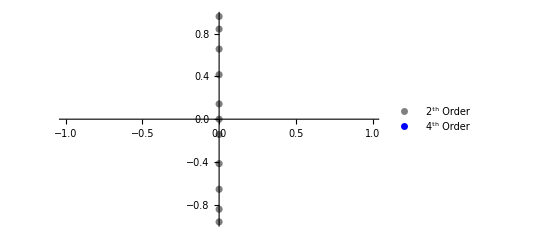
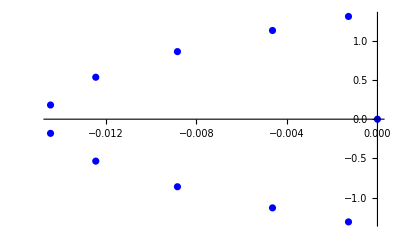
Show[-Graphics-,-Graphics-,ComplexListPlot[vals6,AspectRatio→1/GoldenRatio,PlotRange→All,PlotLabel→Eigenvalues of Div6-nondiag,PlotStyle→Green,PlotLegends→{6^th Order}],ComplexListPlot[vals8,AspectRatio→1/GoldenRatio,PlotRange→Automatic,PlotLabel→Eigenvalues of Div8-nondiag,PlotStyle→Red,PlotLegends→{8^th Order}],AspectRatio→1/GoldenRatio,PlotRange→All]

```mathematica
Show[cplot2, cplot4, cplot6, cplot8, AspectRatio->1/GoldenRatio,PlotRange->All]
```

```mathematica
(lvals8=Sort[Eigenvalues[N[DDIV8.grad8]]])//MatrixForm
(lvals6=Sort[Eigenvalues[N[DDIV6.grad6]]])//MatrixForm
(lvals4=Sort[Eigenvalues[N[DDIV4.grad4]]])//MatrixForm
(lvals2=Sort[Eigenvalues[N[DDIV2.grad2]]])//MatrixForm
```

Eigenvalues[1]
 |  |  |  |

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Eigenvalues[Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.75,0.15,0.733333,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.15,-0.766667,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}]

(-2.87772
-1.76847
-1.70501
-1.30225
-1.18372
-0.772695
-0.591491
-0.323591
-0.210974
-0.105241
-3.37886×10^-16)

(-1.63191
-1.04512
-0.943575
-0.84777
-0.712836
-0.575441
-0.419651
-0.291369
-0.157626
-0.0787791
4.32117×10^-17)

```mathematica
eigenfunc=DSolve[{D[ψ[x],{x,2}]+(2l+2)/x ψ'[x]+k^2 ψ[x]==0},ψ[x],x]/.C[2]->0
```

{{ψ[x]→(ⅇ^(-ⅈ k x) C[1])/x}}

```mathematica
g=ψ[x]/.eigenfunc[[1]][[1]]
```

(ⅇ^(-ⅈ k x) C[1])/x

```mathematica
Reduce[x^(1/2 (-1-2 l)) BesselJ[1/2 (1+2 l),k x]==0&&l>0 &&x>0,k]
```

False

```mathematica
plot8=Plot[lvals8,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic},PlotLabel->"8th Order"];
```

```mathematica
plot6=Plot[lvals6,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic},PlotLabel->"6th Order"];
```

```mathematica
plot4=Plot[lvals4,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic},PlotLabel->"4th Order"];
```

```mathematica
(cvals4=Eigenvalues[div4.grad4]) // MatrixForm//N;
```

```mathematica
plot2=Plot[lvals2,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

```mathematica
plot4c=Plot[cvals4,{x,.2,1},PlotStyle->Blue,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

```mathematica
Show[plot4c,plot4];
```

```mathematica
Show[plot0,plot4]
```

-Graphics-

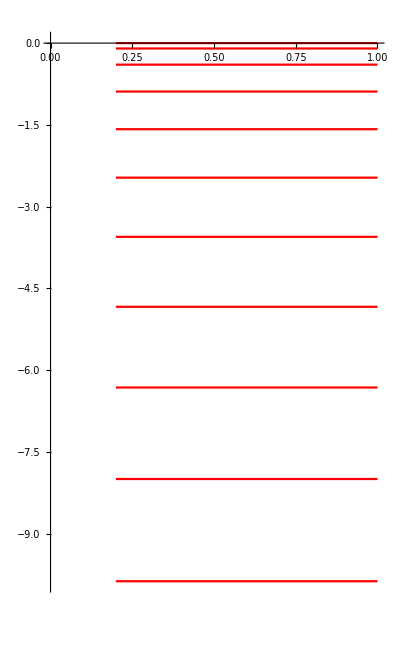

```mathematica
Show[plot0, plot6]
```

```mathematica
Show[plot0, plot8]
```

-Graphics-

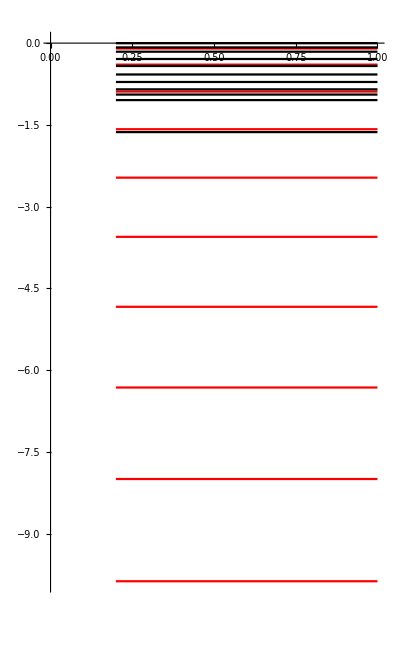

```mathematica
Show[plot0,plot2]
```

```mathematica
(vecs2=Eigensystem[N[DDIV6.grad6]])//MatrixForm;
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
vecs2[[1]]//MatrixForm
vecs2[[2]]//MatrixForm
```

Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.75,0.15,0.733333,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.15,-0.766667,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}

Part::partw: Part 2 of Eigensystem[Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},«9»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{«1»}.(QV/.{}⟦1⟧).{«1»}] does not exist.

Eigensystem[Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.75,0.15,0.733333,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.15,-0.766667,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}]⟦2⟧

```mathematica
ListLinePlot[vecs2[[2]][[;;,1]]]
```

Part::partw: Part 2 of Eigensystem[Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},«9»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{«1»}.(QV/.{}⟦1⟧).{«1»}] does not exist.

Part::partd: Part specification «1»⟦1;;All,1⟧ is longer than depth of object.

Part::partw: Part 2 of Eigensystem[Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},«9»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{«1»}.(QV/.{}⟦1⟧).{«1»}] does not exist.

ListLinePlot::lpn: «1»⟦1;;All,1⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[Eigensystem[Inverse[{{q[1.],q[1.,2.],q[1.,3.],q[1.,4.],q[1.,5.],0.,0.,0.,0.,0.,0.},{q[1.,2.],q[2.],q[2.,3.],q[2.,4.],q[2.,5.],0.,0.,0.,0.,0.,0.},{q[1.,3.],q[2.,3.],q[3.],q[3.,4.],q[3.,5.],0.,0.,0.,0.,0.,0.},{q[1.,4.],q[2.,4.],q[3.,4.],q[4.],q[4.,5.],q[4.,6.],0.,0.,0.,0.,0.},{q[1.,5.],q[2.,5.],q[3.,5.],q[4.,5.],q[5.],q[5.,6.],q[5.,7.],0.,0.,0.,0.},{0.,0.,0.,q[4.,6.],q[5.,6.],q[6.],q[6.,7.],q[6.,8.],0.,0.,0.},{0.,0.,0.,0.,q[5.,7.],q[6.,7.],q[7.],q[7.,8.],0.,0.,0.},{0.,0.,0.,0.,0.,q[6.,8.],q[7.,8.],q[8.],0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,q[9.],0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,q[10.],0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,q[11.]}}/.{}⟦1⟧].{{0.,1.5,-0.3,0.0333333,0.,0.,0.,0.,0.,0.,0.},{0.,-0.15,0.766667,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.,-0.733333,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{0.,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}.(QV/.{}⟦1⟧).{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.75,0.15,0.733333,-0.15,0.0166667,0.,0.,0.,0.,0.,0.},{0.15,-0.766667,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.,0.},{-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.,0.},{0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.,0.},{0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.,0.},{0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667,0.},{0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15,0.0166667},{0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75,-0.15},{0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.,0.75},{0.,0.,0.,0.,0.,0.,0.,-0.0166667,0.15,-0.75,0.}}]⟦2⟧⟦1;;All,1⟧]

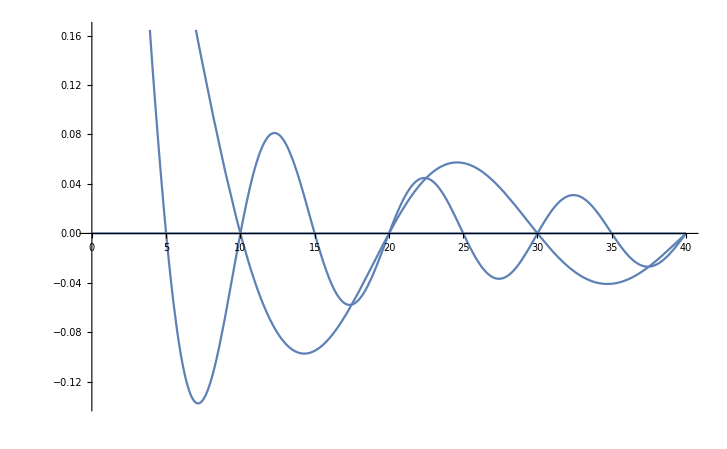

```mathematica
Plot[x^(1/2 (-1-2 l)) BesselJ[1/2 (1+2 l),kk[[1;;3]] x],{x,0,40}]
```